# Classification of images from the web

## Basic example of downloading images from the web and doing classifications

## Wednesday

Anton Antonov
Digital Humanities at Oxford Summer School 2017
July 2017

## Mission statement

With this notebook we show how to obtain, prepare, and do classification experiments with a curated database of images from the Web.

Secondary goal is to compare different classifiers.

The section “NNMF basis” follows the Markdown document “Handwritten digits classification by matrix factorization” from MathematicaVsR at GitHub.

## UCI Li photograph

Actually this page is better. Also see this page.

```mathematica
dirName="/Users/yaman/Downloads/Anton-notebooks-DHOxSS-2017/li_photograph/";
```

```mathematica
annotationText=ReadList[dirName<>"annotation.txt",String];
```

```mathematica
ColumnForm[annotationText⟦1;;4⟧] (*ilk dort row*)
```

0 1/10000.jpg	  flower
1 1/10001.jpg	  maple leaves
2 1/10002.jpg	  flower
3 1/10003.jpg	  flower

```mathematica
annotations=Map[StringCases[#,n:(DigitCharacter..)~~(WhitespaceCharacter..)~~name:(Except[WhitespaceCharacter]..)~~(WhitespaceCharacter..)~~class:(___):>{n,name,class}]⟦1⟧&,annotationText];
Dimensions[annotations]
```

{2360,3}

```mathematica
{2360,3}
annotations
```

{2360,3}

{{0,1/10000.jpg,flower},{1,1/10001.jpg,maple leaves},{2,1/10002.jpg,flower},{3,1/10003.jpg,flower},{4,1/10004.jpg,flower},{5,1/10005.jpg,flower},2348,{2354,5/50089.jpg,coast},{2355,5/50090.jpg,sheep},{2356,5/50091.jpg,sheep},{2357,5/50092.jpg,sheep},{2358,5/50093.jpg,sheep},{2359,5/50094.jpg,sheep}}
 |  |  |  |

```mathematica
RecordsSummary[annotations⟦All,3⟧]⟦1⟧
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Symbol[]
```

```mathematica
imageSubDirName=dirName<>"image.cd/"
```

/Users/yaman/Downloads/Anton-notebooks-DHOxSS-2017/li_photograph/image.cd/

```mathematica
"/Users/yaman/Downloads/Anton-notebooks-DHOxSS-2017/li_photograph/image.cd/"
```

```mathematica
AbsoluteTiming[
images=Map[Import[imageSubDirName<>#⟦2⟧]&,annotations]; (*comcreateing the images. takes the second element and glues them*)
]
```

{253.735,Null}

```mathematica
AbsoluteTiming[
images=ConformImages[images]; (*fotolari sekilleyebiliyormusuz bu functionla*)
]
```

{5.48999,Null}

```mathematica
Tally[ImageDimensions/@images]
```

{{{384,256},2360}}

```mathematica
{{{384,256},2360}}
```

```mathematica
{{{384,256},2360}}
Length[images]
```

{{{384,256},2360}}

2360

```mathematica
data=
Thread[
images->
Map[Which[
#=="flower"||#=="water plant, flower","flower",
#=="firework",#,
True,"other"
]&,annotations⟦All,3⟧]
]; (*BURDA HATA VERIYOR! CRASH YAPIYOR*)
```

```mathematica
RandomSample[data,6]
```

RandomSample::lrwl: The set of items to sample from, data, should be a non-empty list or a rule weights -> choices.

RandomSample[data,6]

```mathematica
trainingInds=Flatten@Map[(pos=Flatten[Position[data⟦All,2⟧,#]];RandomSample[pos,Round[0.7Length[pos]]])&,Union[data⟦All,2⟧]];
testInds=Complement[Range[Length[data]],trainingInds];
```

```mathematica
Length/@{trainingInds,testInds}
```

{1653,707}

```mathematica
Tally[data⟦All,-1⟧]
```

{{flower,385},{other,1907},{firework,68}}

```mathematica
If[True,
data⟦All,1⟧=ConformImages[data⟦All,1⟧,{56,56},ColorSpace->"Grayscale"];
]
```

#### With a "NeuralNetwork" classifier

```mathematica
AbsoluteTiming[
flowerFunc=Classify[data⟦trainingInds⟧,Method->"NeuralNetwork"]
]
```

{5.6196,ClassifierFunction[…]}

```mathematica
AbsoluteTiming[
cm=ClassifierMeasurements[flowerFunc,data⟦testInds⟧]
]
```

{0.114986,ClassifierMeasurementsObject[…]}

```mathematica
cm[{"Accuracy","Precision","Recall"}]
```

{0.810467,<|firework→0.642857,flower→0.459184,other→0.872269|>,<|firework→0.45,flower→0.391304,other→0.907343|>}

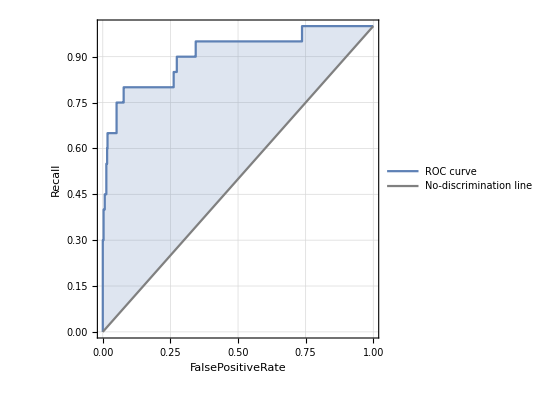
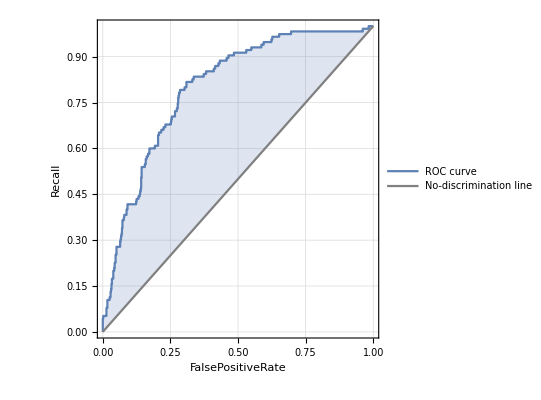
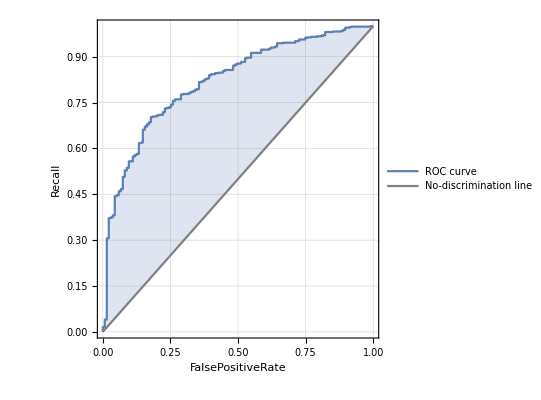
{<|firework→-Graphics-,flower→-Graphics-,other→-Graphics-|>}

```mathematica
cm[{"ROCCurve"}]
```

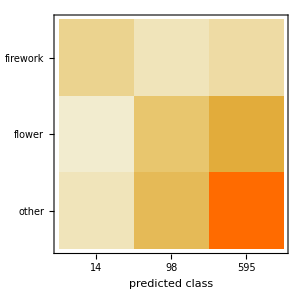

```mathematica
cm["ConfusionMatrixPlot"]
```

#### With a “NearestNeighbors” classifier

```mathematica
AbsoluteTiming[
flowerFunc=Classify[data⟦trainingInds⟧,Method->"NearestNeighbors"]
]
```

{5.20248,ClassifierFunction[…]}

```mathematica
AbsoluteTiming[
cm=ClassifierMeasurements[flowerFunc,data⟦testInds⟧]
]
```

{0.134498,ClassifierMeasurementsObject[…]}

```mathematica
cm[{"Accuracy","Precision","Recall"}]
```

{0.811881,<|firework→Indeterminate,flower→0.5,other→0.818182|>,<|firework→0.,flower→0.0608696,other→0.991259|>}

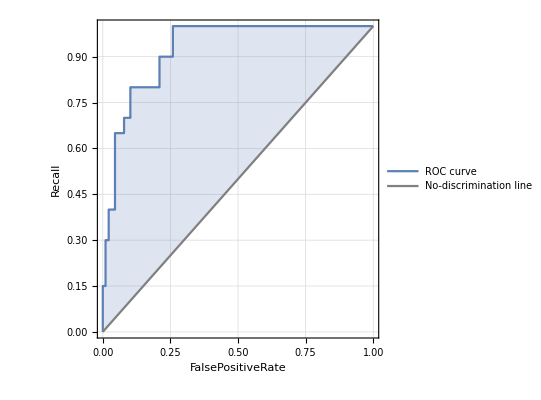
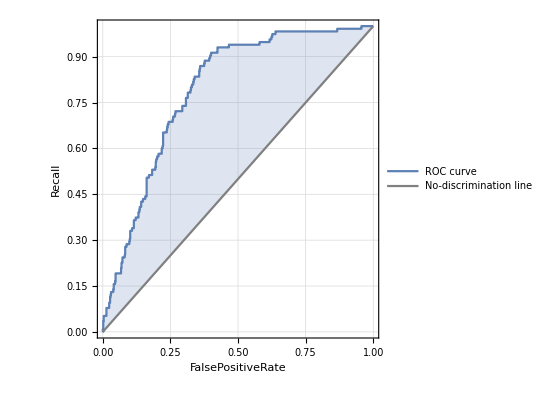
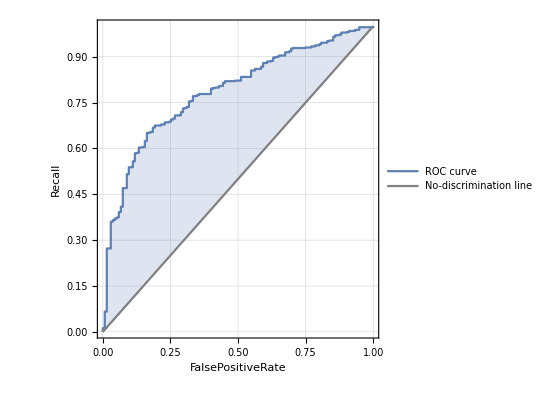
{<|firework→-Graphics-,flower→-Graphics-,other→-Graphics-|>}

```mathematica
cm[{"ROCCurve"}]
```

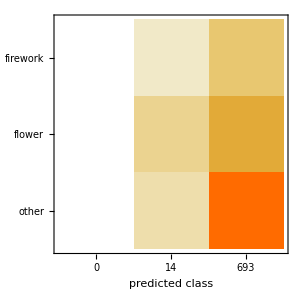

```mathematica
cm["ConfusionMatrixPlot"]
```

## NNMF basis

Here we follow the Markdown document “Handwritten digits classification by matrix factorization” from MathematicaVsR at GitHub.

### Getting data

```mathematica
Reverse@Sort@Select[Tally[annotations⟦All,3⟧],#⟦2⟧>20&]
```

{{water, sea otter,41},{water plant, flower,57},{water plant,41},{water,22},{tree,33},{snow mountain,41},{rock, water,21},{rock, tree, bald eagle,21},{rock, bird,41},{plant,42},{leaves,23},{ice, water,24},{iceberg, water, snow mountain,21},{grass land, animal, bear,23},{glacier, snow,37},{glacier,24},{flower,328},{firework,68},{boat,22},{bird, water, grass,30},{bird, water,43},{bird,42}}

```mathematica
data=Thread[images->Map[Which[#=="flower"||#=="water plant, flower","flower",#=="firework",#,True,"other"]&,annotations⟦All,3⟧]];
```

```mathematica
trainImages=ConformImages[data⟦trainingInds,1⟧,{56,56},ColorSpace->"Grayscale"];
trainImagesLabels=data⟦trainingInds,2⟧;
```

```mathematica
RandomSample[trainImages,12]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[trainImagesLabels,12]
```

{flower,other,other,other,flower,flower,other,other,other,flower,other,flower}

```mathematica
testImages=ConformImages[data⟦testInds,1⟧,{56,56},ColorSpace->"Grayscale"];
testImagesLabels=data⟦testInds,2⟧;
```

### Linear vector space representation

```mathematica
trainImagesMat=N@SparseArray[Flatten@*ImageData/@trainImages]
```

SparseArray[<5180515>, {1653, 3136}]

```mathematica
testImagesMat=N@SparseArray[Flatten@*ImageData/@testImages]
```

SparseArray[<2215256>, {707, 3136}]

```mathematica
classLabels=Union[trainImagesLabels,testImagesLabels]
```

{firework,flower,other}

### The matrix factorization

```mathematica
nBasisSize=40;
AbsoluteTiming[
nnmfRes=ParallelMap[Function[{cl},Print[Style[cl,Bold,Red]];
pos=Flatten@Position[trainImagesLabels,cl];
tmat=trainImagesMat[[pos,All]];
res=GDCLS[tmat,nBasisSize,PrecisionGoal->4,"MaxSteps"->20,"RegularizationParameter"->0.1,"PrintProfilingInfo"->False];
bres=RightNormalizeMatrixProduct@@res;
Join[bres,{(Norm/@res[[2]])/(Norm/@bres[[2]]),PseudoInverse[bres[[2]]],tmat}]],classLabels,DistributedContexts->Automatic];
nnmfRes=AssociationThread[classLabels->nnmfRes];]
```

firework

flower

other

{170.249,Null}

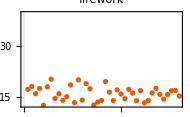
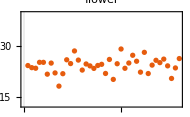
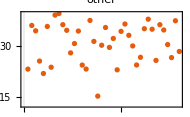
-Graphics- | -Graphics- | -Graphics-
 |  | 
 |  | 
 |  |

```mathematica
Grid[ArrayReshape[#,{4,3},""]&@Map[ListPlot[nnmfRes[#][[3]],PlotRange->MinMax[Flatten@Normal@Values[nnmfRes][[All,3]]],PlotStyle->PointSize[0.02],PlotTheme->"Scientific",ImageSize->190,PlotRange->All,PlotLabel->#]&,Keys[nnmfRes]]]
```

```mathematica
Magnify[#,1.6]&@Grid[Partition[#,10]&@Map[ImageAdjust@Image@Partition[#,56]&,nnmfRes["flower"][[2]]],Dividers->All,FrameStyle->GrayLevel[0.7]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Classification functions

```mathematica
Clear[NNMFClassifyImageVector]
Options[NNMFClassifyImageVector]={"PositiveDifference"->False,"NumberOfNNs"->4,"WeightedNNsAverage"->False,"RepresentationNorm"->False};
NNMFClassifyImageVector[factorizationRes_Association,vec_?VectorQ,opts:OptionsPattern[]]:=Block[{residuals,invH,nW,nf,approxVec,scores,pos,rv,nnns=OptionValue["NumberOfNNs"],inds,ws},residuals=Map[(invH=factorizationRes[#][[4]];
(*nW=(#/Norm[#])&/@factorizationRes[#]⟦1⟧;*)nf=Nearest[factorizationRes[#][[1]]->Range[Dimensions[factorizationRes[#][[1]]][[1]]]];
If[TrueQ[OptionValue["RepresentationNorm"]],approxVec=vec.invH;
CosineDistance[Flatten[factorizationRes[#][[1]][[nf[approxVec]]]],approxVec],(*ELSE*)inds=nf[vec.invH,OptionValue["NumberOfNNs"]];
If[TrueQ[OptionValue["WeightedNNsAverage"]],ws=Map[Norm[vec-#]&,(factorizationRes[#][[5]])[[inds]]];
approxVec=ws.(factorizationRes[#][[5]])[[inds]],(*ELSE*)approxVec=Total[(factorizationRes[#][[5]])[[inds]]]];
rv=vec/Norm[vec]-approxVec/Norm[approxVec];
If[TrueQ[OptionValue["PositiveDifference"]],rv=Clip[rv,{0,∞}]];
Norm[rv]])&,Keys[factorizationRes]];
{Keys[factorizationRes][[Position[residuals,Min[residuals]][[1,1]]]],AssociationThread[Keys[factorizationRes]->residuals]}];
```

### Classification

```mathematica
AbsoluteTiming[nnmfClResInv=ParallelMap[NNMFClassifyImageVector[nnmfRes,#,"RepresentationNorm"->False,"NumberOfNNs"->30,"WeightedNNsAverage"->False]&,#&/@testImagesMat];]
```

{5.78741,Null}

```mathematica
nnmfClResDT=Transpose[{testImagesLabels,nnmfClResInv[[All,1]]}];
```

#### Total accuracy

```mathematica
N@Mean[(Equal@@@nnmfClResDT)/.{True->1,False->0}]
```

0.746818

#### Precision per class

```mathematica
t=Map[Association@Flatten@{"Label"->#[[1,1]],"NImages"->Length[#],"Precision"->N@Mean[(Equal@@@#)/.{True->1,False->0}]}&,GatherBy[nnmfClResDT,First]];
t=SortBy[t,First];
Dataset[t]
```

Dataset[<>]

#### ROC curve

Fairly complicated to computer here!

```mathematica
thRange=Range[0,1,0.025];
```

```mathematica
aROCs=
Association@
Table[(
nonTargetClass="Non"<>targetClass;
targetClass->
Table[(
mf=Join[AssociationThread[classLabels->Table[1,Length[classLabels]]],<|targetClass->th|>];
clRes=Map[Merge[{mf,#},Times@@#&]&,nnmfClResInv⟦All,2⟧];
cres=Position[#,Min[#]]⟦1,1,1⟧&/@clRes;
cres=If[#==targetClass,#,nonTargetClass]&/@cres;
ToROCAssociation[{targetClass,nonTargetClass},Map[If[#==targetClass,#,nonTargetClass]&,testImagesLabels],cres]),{th,thRange}]),
{targetClass,classLabels}
];
```

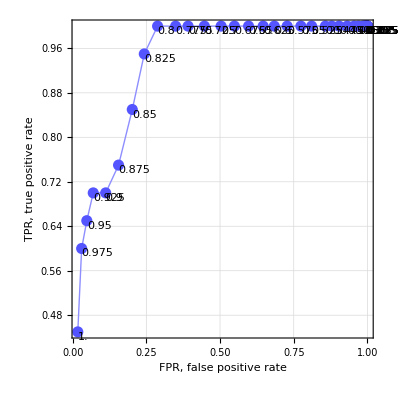
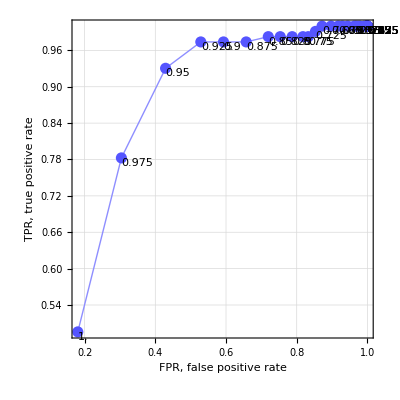
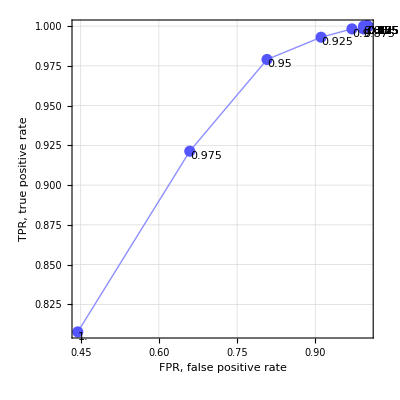
<|firework→-Graphics-,flower→-Graphics-,other→-Graphics-|>

```mathematica
AssociationMap[ROCPlot[thRange,aROCs[#],"PlotJoined"->Automatic,GridLines->Automatic]&,Keys[aROCs]]
```

## Getting artsy

See https://mathematica.stackexchange.com/a/141277/34008 .

### Adapter

```mathematica
Tally[#⟦3⟧=="flower"&/@annotations]
```

{{True,328},{False,2032}}

```mathematica
mnistLikeDigits=ConformImages[Pick[images,#⟦3⟧=="flower"&/@annotations],{56,56},ColorSpace->"Grayscale"];
```

```mathematica
Tally[ImageDimensions/@mnistLikeDigits]
```

{{{56,56},328}}

```mathematica
RandomSample[mnistLikeDigits,12]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sort[mnistLikeDigits]
```

### GAN

```mathematica
ClearAll[progressFuncCreator]
progressFuncCreator[rands_List]:=Function[{reals},ImageResize[NetDecoder[{"Image","Grayscale"}][NetExtract[#Net,"gen"][reals]],50]]/@rands&
```

```mathematica
trainingData=<|"random"->RandomInteger[{1,10},Length[mnistLikeDigits]],"Input"->Map[RandomReal[{-0.05,0.05},{1,28,28}]+ArrayReshape[ImageData[#],{1,28,28}]&,mnistLikeDigits]|>;
generator=NetChain[{EmbeddingLayer[8*6*6,10],ReshapeLayer[{8,6,6}],DeconvolutionLayer[8,4,"Stride"->2],Ramp,DeconvolutionLayer[1,4,"Stride"->2,"PaddingSize"->1],LogisticSigmoid}];
discriminator=NetChain[{ConvolutionLayer[4,4],Tanh,PoolingLayer[3,1],16,Ramp,1},"Input"->{1,28,28}];
wganNet=NetGraph[<|"gen"->generator,"discrimop"->NetMapOperator[discriminator],"cat"->CatenateLayer[],"reshape"->ReshapeLayer[{2,1,28,28}],"flat"->FlattenLayer[],"total"->SummationLayer[],"scale"->ConstantTimesLayer["Scaling"->{-1,1}]|>,{NetPort["random"]->"gen"->"cat",NetPort["Input"]->"cat","cat"->"reshape"->"discrimop"->"flat"->"scale"->"total"},"Input"->{1,28,28}];
NetTrain[wganNet,trainingData,"Output",Method->{"ADAM","Beta1"->0.5,"LearningRate"->0.01,"WeightClipping"->{{"discrimop",1}->1,"discrimop"->0.001}},TrainingProgressReporting->{progressFuncCreator[Range[10]],"Interval"->Quantity[0.3,"Seconds"]},LearningRateMultipliers->{"scale"->0,"gen"->-0.05},BatchSize->32,MaxTrainingRounds->5000];
```